# A Minimal Metamodel for the Foundations of Medicine

# Towards a Formalized Theory for the Foundations of Medicine

[Indicate “symptoms” by a different outline, with the “healthy” outline indicated]

Add a real “with treatment case:

```mathematica
healers = HealCA[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {110, {-110, 110}},<|{23,111}->2|>, All, 98 < # < 105&];
```

```mathematica
healers[[16]]
```

<|{37,107}→3|>

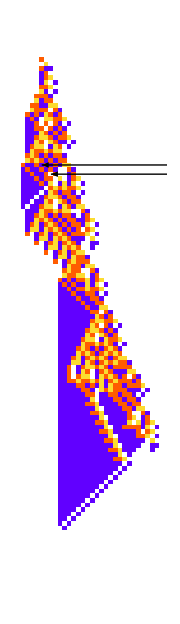
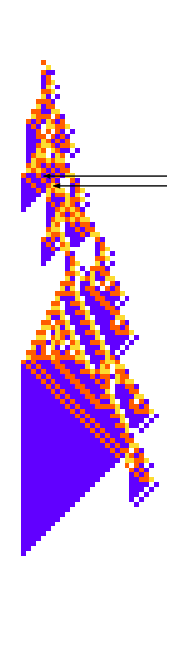
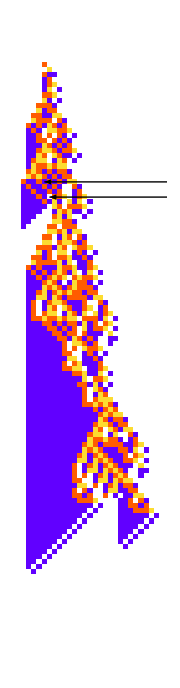
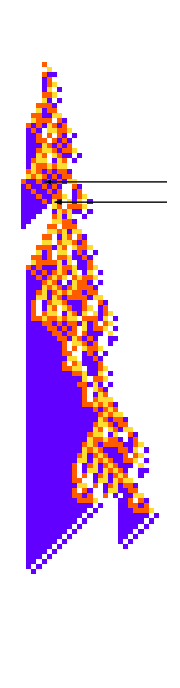
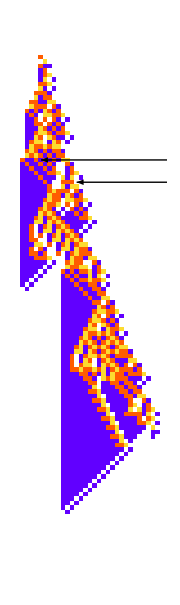
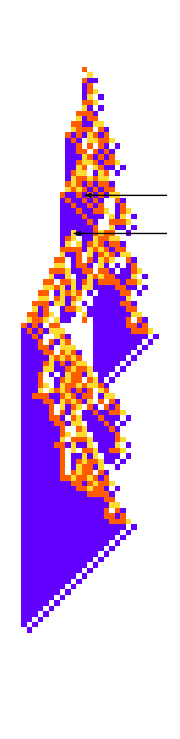
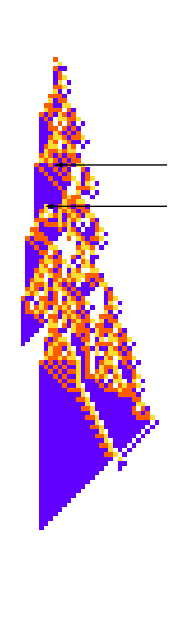
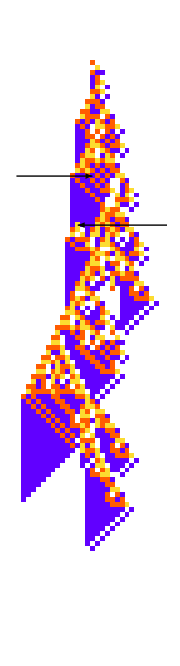

```mathematica
Table[
PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {110, {-110, 110}},Join[<|{23,111}->2|>, healers[[i]]]]], {i, 32}]
```

```mathematica
GraphicsRow[Labeled[Function[u,If[#2==="diseased",Show[u,Graphics[{EdgeForm[Directive[Thick, Dotted]],Opacity[0.4,Transparent](*Transparent*),CAPolygon[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {110, {-6, 216}},<||>]]}]],u]]@PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {110,{-110, 110}},#1],ImageSize->{Automatic,500}, "Trim"->{3, None}], #2]&@@@{{<||>, "healthy"},{<|{23,111}->2|>, "diseased"},{<|{23,111}->2,{25,113}->3|>, "with treatment"}} ]
```

-Graphics-

## A Theory of Medicine?

As it’s practiced today, medicine is almost always about particulars: “this has gone wrong; this is how to fix it”.  But might it also be possible to talk about medicine in a more general, more abstract way---and perhaps to create a framework in which one can study its essential features without engaging with all of its details?

My goal here is to take the first steps towards such a framework.  And in a sense my central result is that many broad phenomena in medicine seem at their core to be fundamentally computational---and to be captured by remarkably simple computational models that are readily amenable to study by computer experiment.

I should make it clear at the outset that I’m not trying to set up a specific model for any particular aspect or component of biological systems.  Rather, my goal is to “zoom out” and create what one can think of as a “metamodel” for studying and formalizing the abstract foundations of medicine.

What I’ll be doing builds on my recent work on using the computational paradigm to study the foundations of biological evolution.  And indeed in constructing idealized organisms we’ll be using the very same class of computational models.  But now, instead of considering idealized genetic mutations and asking what types of idealized organisms they produce, we’re going to be looking at specific evolved idealized organisms, and seeing what effect perturbations have on them.  Roughly, the idea is that an idealized organism will operate in its normal “healthy” way if there are no perturbations---but perturbations can “derail” the operation of the organism and introduce what we can think of as “disease”. And with this setup we can then think of the “fundamental problem of medicine” as being the identification of additional perturbations that can “treat the disease” and put the organism at least approximation back on its normal “healthy” track.

As we’ll see, most perturbations lead to lots of detailed changes in our idealized organisms, much as perturbations in biological organisms normally lead to vast numbers of effects, say at a molecular level.  But as in medicine, we can imagine that all we can observe (and perhaps all we care about) are certain coarse-grained “symptoms”.  And the fundamental problem of medicine is then to work out from these symptoms what “treatment” (if any) will end up being useful.

It’s worth emphasizing again that we’re not trying here to derive specific, actionable, medical conclusions.  Rather, my goal is to build a conceptual framework in which, for example, all sorts of widespread phenomena in medicine that in the past have seemed at best vague and anecdotal can begin to be formalized and studied in a systematic way.  At some level, it’s a bit like what Darwinism brought to biological evolution.  But in modern times there’s a critical new element: the computational paradigm, which not only introduces all sorts of powerful new theoretical concepts, but also leads us to the practical new methodology of computer experimentation.  And indeed much of what follows will be based on the (often surprising) results of computer experiments that will allow us to progressively build our intuition---and structure our thinking---about fundamental phenomena in medicine.

## A Minimal Metamodel

How can we make a metamodel of medicine?  We need an idealization of biological organisms and their behavior and development.   We need an idealization of the concept of disease for such organisms.  And we need an idealization of the concept of treatment.

For our idealization of biological organisms we’ll use a class of simple computational systems called cellular automata (that I happen to have studied since the early 1980s).  Here’s a specific example:

Would be nice to use a less hacky RulePlot solution

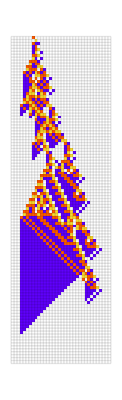
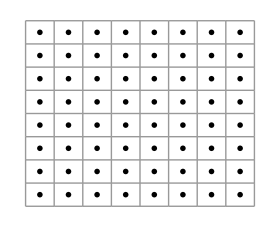

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},110],{{0,0},{3,3}}],ColorRules->colorrules,ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.1]],RulePlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1}],ColorRules->colorrules][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

What’s going on here is that we’re progressively constructing the pattern on the left (representing the development and behavior of our organism) by repeatedly applying the rules on the right (representing the idealized genome---and other biochemical, etc. rules---of our organism).  Roughly we can think of the pattern on the left as corresponding to the “life history” of our organism---growing, developing and eventually dying as it goes down the page.  And even though there’s a rather organic look to the pattern, remember that the system we’ve set up isn’t intended to provide a model for any particular real-world biological system.  Rather, the goal is just for it to capture enough of the foundations of biology that it can serve as a successful metamodel to let us explore our questions about the foundations of medicine.

Looking at our model here in more detail, we see that it involves a grid of squares---or “cells” (computational, not biological)---each having one of 4 possible colors (white and three others).  We start from a single red “seed” cell on the top row of the grid, then compute the colors of cells on subsequent steps (i.e. on subsequent rows down the page) by successively applying the rules on the right.  The rules here are basically very simple.  But we can see that when we run them they lead to a fairly complicated pattern---which in this case happens to “die out” (i.e. all cells become white) after exactly 101 steps.

So what happens if we perturb this system?  On the left here we’re showing the system as above, without perturbation. But on the right we’re introducing a perturbation by changing the color of a particular cell (on step 16)---leading to a rather different (if qualitatively similar) pattern:

Look for different example!!  Make the cell flip be to a color not white
Align everything at the top.  Indicate the magnification area
Put extra space on the left/right edges

```mathematica
, Dashed, Line[{{0, 105 -8 },{0, 105+1}}], Line[{{15, 105 - 8},{29, 105+1}}]
```

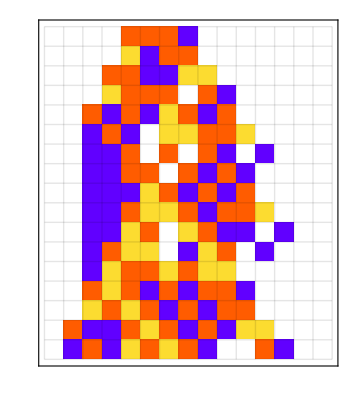
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[With[{ru={299459058088077823758143088095350287424,4,1},pt=<|{15,206}->0|>},{
PlotCA[PerturbedCellularAutomaton[ru,{{1},0},{{8, 24},{-200,200}},<||>],"MaxWidth"->{196, 210}, "Trim"->{None, None},ImageSize->{Automatic,150},Mesh->All,MeshStyle->Opacity[.1], Frame->True],
PlotCA[PerturbedCellularAutomaton[ru,{{1},0},{105,{-200,200}},{}],"MaxWidth"->{196, 225}, "Trim"->{None, None},ImageSize->{Automatic,450},Mesh->All,MeshStyle->Opacity[.1],"Graphics"->{ Haloing[], EdgeForm[Black], FaceForm@None, Rectangle[{0, 105 - 8}, {15, 105 - 24}]}](* ]*),
Spacer[20], 
PlotCA[PerturbedCellularAutomaton[ru,{{1},0},{105,{-200,200}},pt],"MaxWidth"->{196, 225}, "Trim"->{None, None},Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,450}, "Graphics"->{ Haloing[], EdgeForm[Black], FaceForm@None, Rectangle[{0, 105 - 8}, {15, 105 - 24}]}],PlotCA[{PerturbedCellularAutomaton[ru,{{1},0},{{8, 24},{-200,200}},{15,206}->0, "ReturnPerturbations"->False],<|{15 - 9 + 1, 206}->0|>},Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,150}, "MaxWidth"->{196, 210}, "Trim"->{None, None}, "ArrowSize"->Large, "ArrowDirection"->"Left", Frame->True],
Spacer[10]}],Alignment->Bottom]
```

Here are the results of some other perturbations to our system:

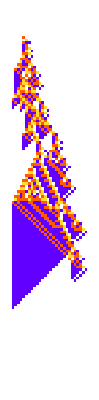
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},Row[Insert[PlotCA[PerturbedCellularAutomaton[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2],Spacer[1]]]
```

Some perturbations (like the one in the second panel here) quickly disappear; in essence the system quickly “heals itself”.  But in most cases even single-cell perturbations like the ones here have a long-term effect.  Sometimes they can “increase the lifetime” of the organism; often they will decrease it.  And sometimes---like in the last case shown here---they will lead to essentially unbounded “tumor-like” growth.

In biological or medical terms, the perturbations we’re introducing are minimal idealizations of “things that can happen to an organism” in the course of its life.  Sometimes the perturbations will have little or no effect on the organism.  Or at least they won’t “really hurt it”---and the organism will “live out its natural life” (or even extend it a bit).  But in other cases, a perturbation can somehow “destabilize” the organism, in effect “making it develop a disease”, and often making it “die before its time”.

But now we can formulate what we can think of as the “fundamental problem of medicine”: given that perturbations have had a deleterious effect on an organism, can we find subsequent perturbations to apply that will serve as a “treatment” to overcome the deleterious effect?

The first panel here shows a particular perturbation that makes our idealized organism die after 47 steps.  And the subsequent panels show various “treatments” (i.e. additional perturbations) that serve at least to “keep the organism alive”:

Fix spacing etc.  [  cases in the middle are close together ; ends are further apart ]
Use (a)  etc.

```mathematica
GraphicsRow[MapThread[Labeled[#1,Text[#2]]&,With[{u=PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {120, {-200, 200}}, #]]&/@{<|{23,202}->3|>,<|{23,202}->3,{57,214}->3|>,<|{23,202}->3,{44,209}->2|>,<|{23,202}->3,{34,208}->3|>,<|{23,202}->3,{26,204}->1|>,<|{23,202}->3,{31,202}->3|>,<|{23,202}->3,{35,207}->3|>,<|{23,202}->3,{52,211}->3|>, <||>}},{u,Take[Alphabet[],Length[u]]}]]]
```

-Graphics-

In the later panels here the “life history” of the organism gets closer to the “healthy” unperturbed form shown in the final panel.  And if our criterion is restoring overall lifetime, we can reasonably say that the “treatment has been successful”.  But it’s notable that the detailed “life history” (and perhaps “quality of life”) of the organism will essentially never be the same as before: as we’ll see in more detail later, it’s almost inevitably the case that there’ll be at least some (and often many) long-term effects of the perturbation+treatment.

So now that we’ve got an idealized model of the “problem of medicine”, what can we say about solving it?  Well, the main thing is that we can get a sense of why it’s fundamentally hard.  And beyond anything else, the central issue is a fundamentally computational one: the phenomenon of computational irreducibility.

Given any particular cellular automaton rule, with any particular initial condition, one can always explicitly run the rule, step by step, from that initial condition, to see what will happen.  But can one do better?  Experience with mathematical science might make one imagine that as soon as one knows the underlying rule for a system, one should in principle immediately be able to “solve the equations” and jump ahead to work out everything about what the system does, without explicitly tracing through all the steps.  But one of the central things I discovered in studying simple programs back in the early 1980s is that it’s common for such systems to show what I called computational irreducibility, which means that the only way to work out their detailed behavior is essentially just to run their rules step by step and see what happens.

So what about biology?  One might imagine that with its incremental optimization, biological evolution would produce systems that somehow avoid computational irreducibility, and (like simple machinery) have obvious easy-to-understand mechanisms by which they operate.  But in fact that’s not what biological evolution typically seems to produce.  And instead---as I’ve recently argued---what it seems to do is basically just to put together randomly found “lumps of irreducible computation” that happen to satisfy its fitness criterion.  And the result is that biological systems are full of computational irreducibility, and mostly aren’t straightforwardly “mechanically explainable”.  (The presence of computational irreducibility is presumably also why theoretical biology based on mathematical models has always been so challenging.)

But, OK, given all this computational irreducibility, how is that medicine is even possible?  How is it that we can know enough about what a biological system will do to be able to determine what treatment to use on it?  Well, computational irreducibility makes it hard.  But it’s a fundamental feature of computational irreducibility that within any computationally irreducible process there must always be pockets of computational reducibility.  And if we’re trying to achieve only some fairly coarse objective (like maximizing overall lifetime) it’s potentially possible to leverage some pocket of computational reducibility to do this.

(And indeed pockets of computational reducibility within computational irreducibility are what make many things possible---including having understandable laws of physics, doing higher mathematics, etc.)

## The Diversity and Classification of Disease

With our simple idealization of disease as the effect of perturbations on the life history of our idealized organism, we can start asking questions like “What is the distribution of all possible diseases?”

And to begin exploring this, here are the patterns generated with a random sample of the 4383 possible single-point perturbations to the idealized organism we’ve discussed above:

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];PerturbedCellularAutomaton[ru,{{1},0},{150,{-8,36}},1]],"Trim"->{None,None},ImageSize->{Automatic,400}],{i,60}],15]]
```

-Graphics-

should that really be   symptomologies ?

Clearly there’s a lot of variation in these life histories---in effect a lot of different symptomatologies.  If we average them all together we lose the detail and we just get something close to the original:

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},PerturbedCellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}, #, "ReturnPerturbations"->False]&/@ allperts[CellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}]]];
```

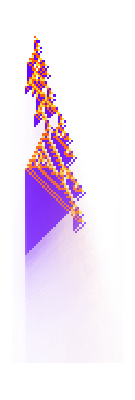

```mathematica
ArrayPlot[Map[Blend[Take[Last/@colorrules,4],BinCounts[#,{0,4,1}]]&,Transpose[pcas,{3,1,2}],{2}]]
```

But if we look at the distribution of lifetimes, we see that while it’s peaked at the original value, it nevertheless extends to both shorter and longer values:

Still to modernize ??

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

```mathematica
lts500=Block[{ru={299459058088077823758143088095350287424,4,1},ca,aps},ca=CellularAutomaton[ru,{{1},0},{500,All}];
aps=allperts[ca,ru[[2]]];
ParallelMap[TestCALifeTime[PerturbCA[{ca,ru},#]]&,aps]];
```

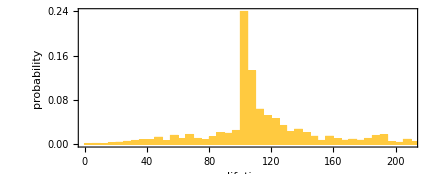

```mathematica
Histogram[lts500, 100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]
```

In medicine (or at least Western medicine) it’s been traditional to classify “things that can go wrong” in terms of discrete diseases.  And we can imagine also doing this in our simple model.  But it’s already clear from the array of pictures above that this is not going to be a straightforward story.  We’ve got a different detailed pattern for every different perturbation.  How should we group them together?

Well---much as in medicine---it depends on what we care about.  In medicine we would talk about symptoms, which in our idealized model we can basically identify with features of patterns.  And as an example, we might decide that the only features that matter are ones associated with the boundary shape of our pattern:

Show this on top of the actual pattern

```mathematica
silhouette[list_,opts___]:=Graphics[{EdgeForm[Gray],LightGray,Polygon[Join[#1,Reverse[#2]]]&@@Transpose[MapIndexed[{#,-First[#2]}&,DeleteCases[list,{}],{2}]]},opts]
```

```mathematica
silhouette[Map[nonzeroRange,getca[{299459058088077823758143088095350287424,4,1}]]]
```

-Graphics-

So what happens to these boundary shapes with different perturbations?  Here are the most frequent shapes found (together with their probabilities):

Show unperturbed as dotted line or something in each case

```mathematica
lts = Block[{ru = {299459058088077823758143088095350287424,4,1}},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas];
```

```mathematica
shapes = Map[nonzeroRange, pcas, {2}];
```

```mathematica
cts=Counts[shapes];
```

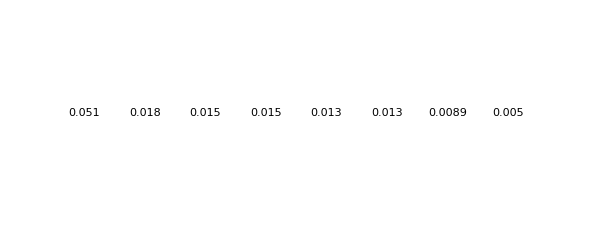

```mathematica
GraphicsRow[KeyValueMap[Labeled[silhouette[#,Frame->True,FrameTicks->None,ImageSize->{Automatic,200},PlotRange->{{190,230},{-120,0}}],Text[NumberForm[N[#2/Total[cts]],2]]]&,Take[ReverseSort[cts],8]]]
```

We might think of these as representing “common diseases” of our idealized organism.  But what if we look at all possible “diseases”---at least all the ones produced by single-cell perturbations?  Using boundary shape as our way to distinguish diseases we find that if we plot the frequency of diseases against their rank we get a rough power law distribution (and, yes, it’s not clear why it’s a power law):

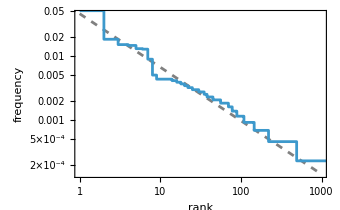

```mathematica
Show[Plot[0.04583459736390076/x^0.8374727002923698,{x,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->Directive[Dashed,Gray],Frame->True,FrameLabel->{"rank","frequency"}],ListStepPlot[Values[ReverseSort[cts]]/Total[Values[cts]],PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{"rank","frequency"}]]
```

What are the “rare diseases” (i.e. ones with low frequency) like?  Their boundary shapes can be quite diverse:

Fix frame escapes

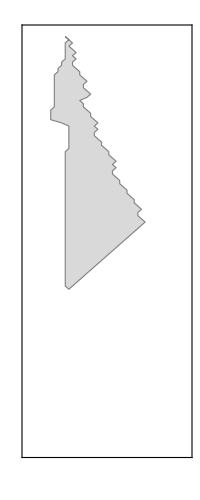
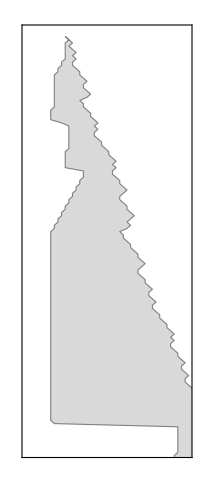
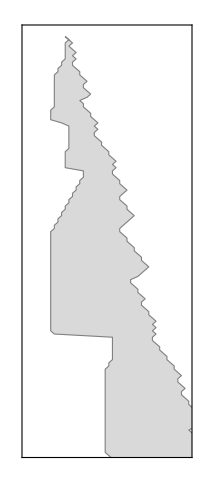
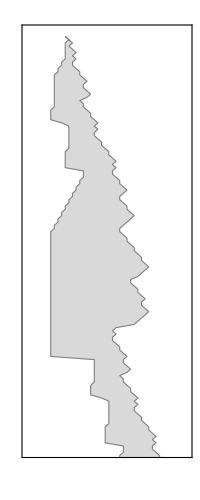
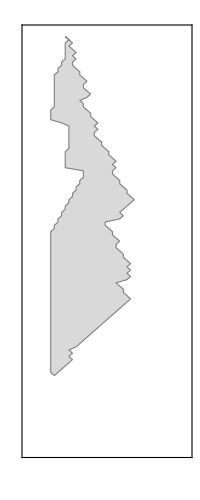
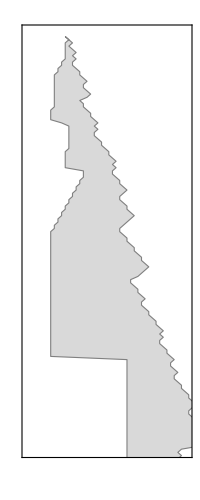
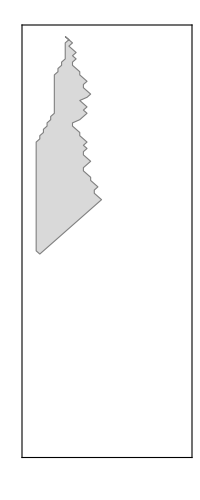
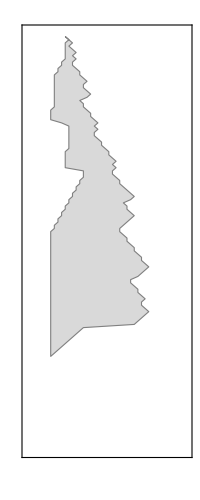

```mathematica
GraphicsGrid[Partition[SeedRandom[6353];silhouette[#,Frame->True,FrameTicks->None,PlotRange->{{190,235},{-130,0}}]&/@Keys[RandomSample[Select[cts,#==1&],60]],20]]
```

But, OK, can we somehow quantify all these “diseases”?  For example, as a kind of “imitation medical test” we might look at how far to the left the boundary of each pattern ever goes.  With single-point perturbations, 84% of the time it’s the same as in the unperturbed case---but there’s a distribution of other, “less healthy” results (here plotted on a log scale)

Mark with dotted line the unperturbed case

```mathematica
LaunchKernels["Local"];
```

```mathematica
pcas=Block[{ru={299459058088077823758143088095350287424,4,1},ca},ca=CellularAutomaton[ru,{{1},0},{400,{-200,200}}];
ParallelMap[PerturbedCellularAutomaton[ru,{{1},0},{400,{-200,200}},#,"ReturnPerturbations"->False]&,allperts[ca,4]]];
```

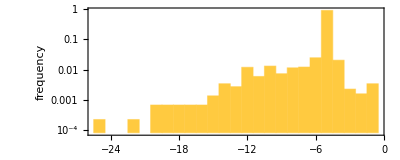

```mathematica
Histogram[-(201-Min[If[Length[#]==1,Infinity,Length[First[#]]]&[Split[#]]&/@#])&/@pcas,{1},{"Log","Probability"},Frame->True,AspectRatio->.4,FrameLabel->{"leftmost offset","frequency"},PlotRange->All]
```

with extreme examples being:

```mathematica
LaunchKernels["Local"];
```

```mathematica
pcas=Block[{ru={299459058088077823758143088095350287424,4,1},ca},ca=CellularAutomaton[ru,{{1},0},{400,{-200,200}}];
ParallelMap[PerturbedCellularAutomaton[ru,{{1},0},{400,{-200,200}},#,"ReturnPerturbations"->False]&,allperts[ca,4]]];
```

```mathematica
lefts=-(201-Min[If[Length[#]==1,Infinity,Length[First[#]]]&[Split[#]]&/@#])&/@pcas;
```

```mathematica
aps=Block[{ru={299459058088077823758143088095350287424,4,1},ca},ca=CellularAutomaton[ru,{{1},0},{400,{-200,200}}];allperts[ca,4]];
```

```mathematica
GraphicsRow[Labeled[Show[PlotCA[PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{200,{-200,200}},#],ImageSize->{Automatic,300}],Graphics[Style[Line[{{21,0},{21,200}}],Dotted]]],Text[#2]]&@@@({aps[[#]],lefts[[#]]}&/@{114,1417,1741,4302,1620,440,1618})]
```

-Graphics-

And, yes, we could diagnose any pattern that goes further to the left than the unperturbed one as a case of, say, “leftiness syndrome”.  And we might imagine that if we set up enough tests, we could begin to discriminate between many discrete “diseases”.  But somehow this seems quite ad hoc.

So can we perhaps be more systematic by using machine learning?  Let’s say we just look each whole pattern, then try to place it in an image feature space, say a 2D one.  Here’s an example of what we get:

Check.  Figure out about widths etc.  (probably OK)

```mathematica
FeatureSpacePlot[RandomSample[pcas,400],LabelingFunction->(PlotCA[#[[;;150]]]&),LabelingSize->50,Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453]
```

-Graphics-

The details of this depend on the particulars of the machine learning method we’ve used (here the default FeatureSpacePlot method in Wolfram Language).  But it’s a fairly robust result that “visually different” patterns end up separated---so that in effect the machine learning is successfully automating some kind of “visual diagnosis”.  And there’s at least a little evidence that the machine learning will identify separated clusters of patterns that we can reasonably identify as “truly distinct diseases”---even as the more common situation is that between any two patterns, there are intermediate ones that aren’t neatly classified as one disease or the other.

Still, somewhat in the style of the human “International Classification of Diseases” (ICD), we can try arranging all our patterns in a hierarchy---though it’s basically inevitable that we’ll always be able to subdivide further, and there’ll never be a clear point at which we can say “we’ve classified all the diseases”.

*** Get examples

By the way, in addition to talking about possible diseases, we can talk about what counts as “healthy”.  We could say that our organism is only “healthy” if its pattern is exactly what it would be without any perturbation (“the natural state”).  But what probably better captures everyday medical thinking is to say that our organism should be considered “healthy” if it doesn’t have symptoms (or features) that we consider bad.  And in particular, at least “after the fact” we might say it must have been healthy if its lifetime turned out to be long.

It’s worth noting that even in our simple model, while there are many perturbations that reduce lifetime, there are also perturbations that increase lifetime.  In the course of biological evolution, genetic mutations of the overall underlying rules for our idealized organism might have managed to achieve a certain longevity.  But the point is that nothing says “longevity perturbations” applied “during the life of the organism” can’t get further---and indeed here are some examples where they do:

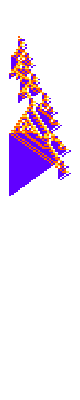
-Graphics-101-Graphics-122-Graphics-140-Graphics-148-Graphics-166-Graphics-157-Graphics-183-Graphics-201

```mathematica
Row[With[{u=PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{205,{-200,200}},#]},Labeled[PlotCA[u,ImageSize->{Automatic,250}],Text[Style[TestCALifeTime[u],Small]]]]&/@{<||>,<|{71,222}->3|>,<|{67,204}->1|>,<|{42,213}->2|>,<|{47,209}->1|>,<|{65,204}->0|>,<|{78,220}->2|>,<|{64,214}->3|>},Spacer[3]]
```

And, actually, in a feature that’s not (at least yet) reflected in human medicine, there are perturbations than can make the lifetime very significantly longer.  And for the particular idealized organized we’re studying here, the most extreme examples obtained with single-point perturbations are:

Halve spacing to make these fit on one line

```mathematica
Row[With[{u=PerturbedCellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},{360,{-200,200}},#]},Labeled[PlotCA[u,ImageSize->{Automatic,300}],Text[Style[TestCALifeTime[First[u]],Small]]]]&/@aps[[Flatten[Reverse[PositionLargest[TestCALifeTime/@pcas,10]]]]],Spacer[.1]]
```

-Graphics-295-Graphics-304-Graphics-305-Graphics-308-Graphics-310-Graphics-320-Graphics-342-Graphics-349-Graphics-354-Graphics-356

OK, but so what happens if we consider perturbations at multiple points?  There are immediately vastly more possibilities than with a single perturbations.  Here are some examples with two perturbations:

Cut off the edges rather than wrapping

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[424324+i];PerturbedCellularAutomaton[ru,{{1},0},{150,{-8,36}},2]],"Trim"->{None,None},ImageSize->{Automatic,400}],{i,30}],15]]
```

-Graphics-

Here with three perturbations:

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[425324+i];PerturbedCellularAutomaton[ru,{{1},0},{150,{-8,36}},3]],"Trim"->{None,None},ImageSize->{Automatic,400}],{i,30}],15]]
```

-Graphics-

And here are examples of what happens when we try to apply five perturbations (though sometimes the organism is “already dead” before we can apply later perturbations):

```mathematica
GraphicsGrid[Partition[Table[PlotCA[With[{ru={299459058088077823758143088095350287424,4,1}},SeedRandom[425324+i];PerturbedCellularAutomaton[ru,{{1},0},{150,{-8,36}},5]],"Trim"->{None,None},ImageSize->{Automatic,400}],{i,30}],15]]
```

-Graphics-

What happens to the overall distribution of lifetimes in these cases?

XXXXX

Of course, in an example of “be careful what you wish for”, perturbations that purely optimize longevity can lead to infinite growth, which indeed “lives long”, but more in the manner of a tumor than what we would normally consider a healthy finite organism:

XXXXXXX

[[ In the computational universe---perhaps like in medicine---things have a habit of being more complicated than one ever imagines.... ]]

One more point is that in what we’ve discussed so far, we’ve only considered “single point” perturbations.  But we can perfectly well also consider perturbations that affect many cells XXXXXXX

XXXXX

## More Perturbations

## Diagnosis & Prognosis

A fundamental objective in medicine is to predict from tests we do or symptoms we observe what will happen.  And, yes, we can now that computational irreducibility will in general make that hard.  But we know from experience that a certain amount of it is possible---which we can interpret as successfully tapping into certain “pockets of computational reducibility”.

<< Correlation between perturbation and actual manifestation >>  << From presentation, can we work out perturbation? >> [[ Only if you’ve been measuring so far ]]

[[ What disease do you have?  At least make a symptom .... ]]
[[ Can we make a diagnosis flow chart? ]]

<<< If we know the whole row of cells it is deterministic >>>

<< ML on width >>

Width < 9 at t=30:

```mathematica
Show[Histogram[Pick[lts,widths[[#,30]]<9&&widths[[#,30]]!=0&/@Range[Length[pcas]]],40,"Probability",PlotRange->{{0,180},Automatic}],Histogram[lts,100,"Probability",ChartStyle->Opacity[.1,Green]]]
```

-Graphics-

```mathematica
Histogram[lts/.-Infinity->225, {1}, "Probability",PlotRange->All,Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]
```

-Graphics-

Survival curve:

```mathematica
Histogram[Flatten[Range/@DeleteCases[lts,-Infinity]],{1},"Probability"]
```

-Graphics-

```mathematica
Table[Block[{ru = {299459058088077823758143088095350287424,4,1}},If[MemberQ[Catenate[bodyidxs[pcas[[i]]]],{35,201}],TestCALifeTime[PerturbCA[ru,Join[aps[[i]],<|{35,201}->3|>]]],Nothing]],{i,Length[aps]}]
```

{100,89,113,84,79,142,79,137,101,136,99,96,66,137,49,186,136,68,119,175,56,62,186,55,122,66,184,123,123,-∞,37,55,92,63,65,66,96,49,108,122,42,52,180,70,51,53,174,87,99,87,80,50,50,163,58,152,51,50,66,-∞,41,96,-∞,101,87,168,125,49,51,107,50,67,53,41,-∞,50,105,158,75,179,98,71,-∞,41,127,41,-∞,98,37,50,76,178,49,49,55,179,177,46,41,101,71,58,148,41,37,-∞,-∞,62,78,96,49,49,157,75,41,104,71,135,188,41,53,125,69,104,109,123,180,46,-∞,-∞,70,58,157,172,150,172,75,133,71,41,51,73,45,137,113,138,182,71,60,43,65,179,180,75,-∞,58,120,75,94,46,172,81,45,50,72,73,198,158,63,177,68,147,113,62,111,60,179,120,75,65,56,80,141,61,152,93,158,124,51,54,103,58,37,108,119,82,94,119,77,95,91,117,86,101,-∞,157,44,49,49,157,58,127,138,170,75,93,70,-∞,166,68,117,75,-∞,93,58,48,46,140,77,135,134,170,170,94,135,87,66,46,66,-∞,156,116,139,161,114,75,154,46,66,46,95,94,170,170,68,77,65,53,117,114,66,138,64,78,150,82,86,119,135,86,134,46,72,46,151,199,65,60,101,111,82,145,55,66,110,97,64,102,135,83,86,135,107,107,151,122,98,-∞,170,133,170,76,-∞,85,99,184,134,56,83,68,186,127,91,97,85,143,-∞,85,85,75,90,91,194,59,120,135,135,97}

```mathematica
Histogram[{Flatten[Range/@DeleteCases[,-Infinity]],Flatten[Range/@DeleteCases[lts,-Infinity]]},{1},"Probability"]
```

-Graphics-

Lifetime given width:

[[ width vs lifetime :   -13.nb ]]

-Graphics-

[[[ Do we go from diagnosis to prognosis, or directly from “measured data”?  ]]]. [[[ The more measurements, the better the prediction ]]]

```mathematica
Plot[PredictorFunction[…][x],{x,0,40}]
```

-Graphics-

## Finding the Best Treatment | AI

<< Put a whole row back to the original and you’ll get the original >>

[[[ Can one find treatment from symptoms? ]]]

<< Going directly to treatment from data , without “identifying a disease” >>

[[ We will model with therapy perturbations ; perhaps drugs can be considered more global ]]

<<< Multiple perturbations >>>. Therapy where you keep on changing values e.g. to emulate what the organism would naturally have done....   [ Can one “hot wire” an organism, to keep going e.g. without expanding .... ]

Clinical trials : given some initial symptom

## The Effect of Genetic Diversity

```mathematica
plotmaskedrule[{299459058088077823758143088095350287424,4,1}]
```

-Graphics-

Overall effect on lifetime:

```mathematica
ParallelMap[Histogram[Module[{ru = #,ca,pcas},
ca = getca[ru];
pcas = Flatten[PerturbAll[{ca, ru}, #]&/@ Flatten[bodyidxs[ca], 1], 1];
TestCALifeTime/@ pcas]/.-Infinity->250, 50, PlotRange->All]&,quickneutral[{299459058088077823758143088095350287424,4,1}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[[[ same analyses; different genomes ]]]

```mathematica
KeyValueMap[Labeled[#1,Text[#2]]&,ReverseSort[Counts[PlotCA[{PerturbCA[#,<|{11,203}->0|>][[;;102]],<|{11,203}->0|>},ImageSize->{Automatic,150}]&/@quickneutral[{299459058088077823758143088095350287424,4,1}]]]]
```

{-Graphics-16,-Graphics-16,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-4,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

## Biological Evolution and the Origins of Our Model Organism

[[ Could be whole organism, or could be e.g. an organ ]]

Picture with  ... nn ...  between breakthroughs

```mathematica
First/@SplitBy[%,Last]
```

{{{0,4,1},0},{{633825300114114700748351602688,4,1},1},{{81763463720033458689778626068480,4,1},2},{{81763463720033458694315185274880,4,1},3},{{81931838076027891908402867077120,4,1},4},{{25967407559121214387661469853159531584,4,1},5},{{25967732077674872814392756608807478336,4,1},6},{{27320406588562325247900243404649442368,4,1},7},{{107074019143647262706119627567490706496,4,1},9},{{128341667036591835415448371735208438848,4,1},12},{{128341667026688315101165329536015445056,4,1},14},{{44247419788783520337962930866412350528,4,1},15},{{44247419788783520337962930866680785984,4,1},37},{{44247257529506691124599539288670497856,4,1},38},{{44247262600109092037517145275483319360,4,1},40},{{44247262614964372508941708574272810048,4,1},49},{{44247282897373976160612132521524096064,4,1},60},{{214388466357843207892299436237408201792,4,1},68},{{214388466357843207892299436237408234560,4,1},84},{{299459058088077823758143088095350287424,4,1},101}}

```mathematica
PlotCA[First[#],"Trim"->{1,5}]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## The Big Picture

[[ other applications ]].   [ Large systems ...  / computer security ]